# LP pricing for the BSM model setting

Working directory for output images.

```mathematica
directory= NotebookDirectory[]<>"images\\" ;
```

In the next cell we set some parameters (that we don' t want to change in the course of our simulation), such as the number of intervals for discretizing our event space (K in the paper), and ranges of our discretization (-6 to 6 of standard normal gaussian distribution).

```mathematica
k = 100;
xmax = 6;
omegas = Range[-xmax, xmax, (2*xmax)/k];
numericalError = 0;
delta = 2*xmax/k;
```

```mathematica
Print[omegas]
```

{-6,-147/25,-144/25,-141/25,-138/25,-27/5,-132/25,-129/25,-126/25,-123/25,-24/5,-117/25,-114/25,-111/25,-108/25,-21/5,-102/25,-99/25,-96/25,-93/25,-18/5,-87/25,-84/25,-81/25,-78/25,-3,-72/25,
-69/25,-66/25,-63/25,-12/5,-57/25,-54/25,-51/25,-48/25,-9/5,-42/25,-39/25,-36/25,-33/25,-6/5,-27/25,-24/25,-21/25,-18/25,-3/5,-12/25,-9/25,-6/25,-3/25,0,3/25,6/25,9/25,12/25,3/5,18/25,21/25,24/25,27/25,6/5,33/25,36/25,39/25,42/25,9/5,48/25,51/25,54/25,57/25,12/5,63/25,66/25,69/25,72/25,3,78/25,81/25,84/25,87/25,18/5,93/25,96/25,99/25,102/25,21/5,108/25,111/25,114/25,117/25,24/5,123/25,126/25,129/25,132/25,27/5,138/25,141/25,144/25,147/25,6}

The following are the default value for the parameters that are going to change in the plots:

```mathematica
mu = 0.5;
sigma = 1;
pi = 10;
strike = 10;
```

These are the possible values of the discretized standard normal distribution.

```mathematica
N[omegas]
Length[omegas]
```

{-6.,-5.88,-5.76,-5.64,-5.52,-5.4,-5.28,-5.16,-5.04,-4.92,-4.8,-4.68,-4.56,-4.44,-4.32,-4.2,-4.08,-3.96,-3.84,-3.72,-3.6,-3.48,-3.36,-3.24,-3.12,-3.,-2.88,-2.76,-2.64,-2.52,-2.4,-2.28,-2.16,-2.04,-1.92,-1.8,-1.68,-1.56,-1.44,-1.32,-1.2,-1.08,-0.96,-0.84,-0.72,-0.6,-0.48,-0.36,-0.24,-0.12,0.,0.12,0.24,0.36,0.48,0.6,0.72,0.84,0.96,1.08,1.2,1.32,1.44,1.56,1.68,1.8,1.92,2.04,2.16,2.28,2.4,2.52,2.64,2.76,2.88,3.,3.12,3.24,3.36,3.48,3.6,3.72,3.84,3.96,4.08,4.2,4.32,4.44,4.56,4.68,4.8,4.92,5.04,5.16,5.28,5.4,5.52,5.64,5.76,5.88,6.}

101

It' s quite Normal...

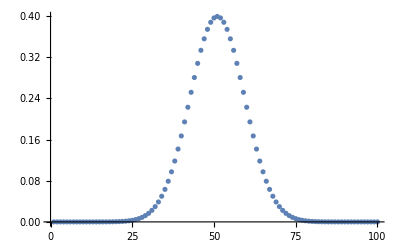

```mathematica
ListPlot[Table[PDF[NormalDistribution[0, 1] , omegas[[i]]] , {i, 1, k}]]
```

### Analytic formula pricing with BSM

Let’s use the formula on Wikipedia to compute the price of a call option in the BSM model. For this we need some helper functions.

```mathematica
analyticPriceBSM[mu_,  spt_, sigma_,strike_,T_,t_,r_ ] :=Module[{d1, d2,value},
d1 = 1/(sigma*Sqrt[T-t])(Log[spt/strike] + (r+(sigma^2/2))*(T-t)   );
d2 = d1 - sigma*Sqrt[T-t];

(* C(S_0, 0) = N(d_1)S_0 - N(d_2)Ke^{e^-r} *)
value=CDF[NormalDistribution[0,1], d1]*spt -  CDF[NormalDistribution[0,1], d2]*strike*Exp[-r(T-t)];
value
] (*Price of the call option in the BSM model*)
```

Example:

```mathematica
N[analyticPriceBSM[mu,  pi, sigma,strike,1,0,0]]
```

3.82925

## LP Pricing BSM

Now let’s use our optimization program to compute the value of the LP.
First, we compute the RN derivative, as we do in the paper in section “Linear programming martingale pricing with the Black-Scholes-Merton model”.

```mathematica
getRadonNikodimDerivative[mu_, omegas_, sigma_] := Module[
{},
Table[Exp[-(mu/sigma)*omegas[[i]] - 1/2(mu/sigma)^2], {i, 1, k}] 
]
getRadonNikodimDerivative[mu, omegas, sigma]
```

{17.7254,16.6932,15.721,14.8055,13.9433,13.1313,12.3666,11.6464,10.9682,10.3295,9.72792,9.16141,8.62789,8.12544,7.65225,7.20662,6.78694,6.3917,6.01947,5.66893,5.3388,5.02789,4.73509,4.45934,4.19965,3.95508,3.72475,3.50784,3.30356,3.11117,2.92999,2.75936,2.59867,2.44734,2.30481,2.17059,2.04419,1.92514,1.81303,1.70745,1.60801,1.51437,1.42618,1.34313,1.26491,1.19125,1.12187,1.05654,0.995012,0.937067,0.882497,0.831104,0.782705,0.737123,0.694197,0.65377,0.615697,0.579842,0.546074,0.514274,0.484325,0.45612,0.429557,0.404542,0.380983,0.358796,0.337902,0.318224,0.299692,0.282239,0.265803,0.250324,0.235746,0.222017,0.209088,0.196912,0.185444,0.174645,0.164474,0.154896,0.145876,0.137381,0.12938,0.121846,0.11475,0.108067,0.101774,0.0958472,0.0902655,0.0850088,0.0800583,0.0753961,0.0710054,0.0668703,0.0629761,0.0593087,0.0558548,0.0526021,0.0495388,0.0466538}

### Regularization method

Let . For BSM, we have . So, let’s impose the constraint  below, where  is the regularization constant.

Below, we define the main function that solves the linear program given the matrices that we construct in the rest of the file. 
	- The first parameters are the parameters of the BSM model and the regularization. 
	- The parameter minmax specifies if you want to solve the minimization or the maximization problem. 
	- tolz is the numerical tolerance of the LP solver that we use
	- methodz is the (classical) algorithm we use for solving the LP. 
	- Setting the parameter outputQ, it can either output the martingale measure, or the price

```mathematica
optimizationPriceBSM[mu_, pi_, sigma_, omegas_,strike_, regularization_, minmax_, outputQ_, tolz_, methodz_]:= Module[
{regularizingMatrix,regularizationVector,ineqMat, ineqVec,
S,sp,mus, pis,p, pNormalized, 
x,dp,derivative,sigmas, eta0},

pis = {1} ~ Join ~{pi};
mus = {0} ~Join~ {mu};
sigmas = {0} ~ Join ~{sigma};

(*Build the payoff matrices and the derivative vector*)
S= Table[  
 Table[
pis[[j]]*Exp[sigmas[[j]]*omegas[[i]] + mus[[j]]  - 1/2sigmas[[j]]^2 ] , 
{i,1, k} ] , {j,1, 2} ]  ;

derivative = Table[Max[  S[[2,i]] - strike,  0], {i, 1, k}];

(* Discretize the probability distribution and normalize it *)
p = Table[PDF[NormalDistribution[0, 1] , omegas[[i]]] , {i, 1, k}];   
pNormalized = p/N[Total[p]];


dp = derivative * pNormalized; (*D[p] in the paper; see Eq.(15)*)
sp = S  * Table[pNormalized, {i, 1, 2}];  (*S[p] in the paper*)
eta0 = mu/sigma*(2*xmax)/k;


regularizingMatrix = DiagonalMatrix[Table[-1, {i, 1,k-1}], 1,k] +(1-eta0)*DiagonalMatrix[Table[1, {i, 1, k}]];
regularizationVector = Table[1/regularization, {i, 1,k-1}] ~ Join ~ {0};

ineqMat = ArrayFlatten[{IdentityMatrix[k], regularizingMatrix, -regularizingMatrix}, 1];
ineqVec = ArrayFlatten[{Table[0, {i, 1, k}]-numericalError, regularizationVector, regularizationVector},1]; 

x =If[minmax,
LinearOptimization[-dp,{ineqMat,ineqVec}, {sp, -pis } , Tolerance->tolz, Method->methodz],    
 LinearOptimization[dp,{ineqMat,ineqVec}, {sp, -pis } , Tolerance->tolz, Method->methodz] ];

If[outputQ,
x,
x.dp
]
]
```

#### We first look at w.r.t. .

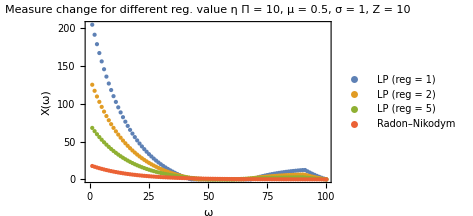

```mathematica
mu = 0.5;
sigma = 1;
pi = 10;
strike = 10;
(*this is the first plot of the paper*)
title ="Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike];
regplot= ListPlot[{optimizationPriceBSM[mu, pi, sigma, omegas,strike,1, True, True, Automatic, Automatic],  
optimizationPriceBSM[mu, pi, sigma, omegas,strike,2, True, True,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,5, True, True, Automatic, Automatic], 
getRadonNikodimDerivative[mu, omegas, sigma]}, 
PlotStyle->PointSize[Medium],
 PlotLegends->Placed[{"LP (reg = 1)", "LP (reg = 2)", "LP (reg = 5)",  "Radon–Nikodym"},{Right, Top}],
LabelStyle->{FontSize->13}, Frame->True,FrameLabel->{"ω", "X(ω)"},
PlotRange->All, 
PlotLabel->"Measure change for different reg. value η\n"<> title,ImageSize->350]
Export[directory <> "regplot.pdf", regplot];
```

It makes sense; being more constrained, the line goes closer to the analytic line. Though I don’t understand why it deviates from two ends.

#### Scanning regularization parameters

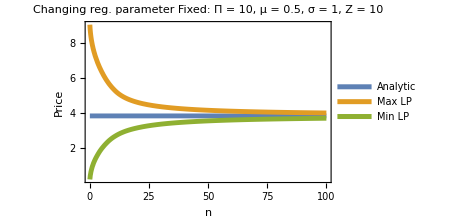

```mathematica
mu = 0.5;
sigma = 1;
pi = 10;
strike = 10;
title ="Changing reg. parameter\n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike];
plt1 =Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, Automatic]}, 
{regularization,0.1, 100}, PlotLegends->Placed[{"Analytic", "Max LP", "Min LP"},{Right, Top}],
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01], Thickness[0.01]},
LabelStyle->{FontSize->13}, Frame->True,
FrameLabel->{"η", "Price"}, 
PlotRange->All, PlotLabel->title,ImageSize->350]
Export[directory <> "plt1.pdf", plt1];
```

#### Scanning the drift (μ) parameter

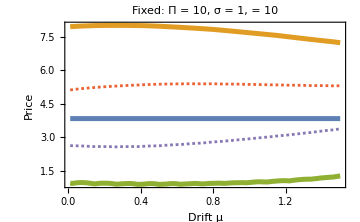

```mathematica
(*Different regularization parameter*)
regularization = 1;
sigma = 1;
pi = 10;
strike = 10;

title ="Fixed: " <> "Π = "  <> ToString[pi]<> ", σ = " <> ToString[sigma] <> ",  = " <> ToString[strike]  ;
pltmu2= Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, Automatic],optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization, False, False,Automatic, Automatic]}, 
{mu,0.01, 1.5},
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01],Dashing[Tiny], Dashing[Tiny]},
 (*PlotLegends->{"Analytic", "Max LP "<>ToString[regularization], "Min LP "<>ToString[regularization],"Max LP "<>ToString[10*regularization], "Min LP "<>ToString[10*regularization]},*)
FrameLabel->{"Drift μ", "Price"}, LabelStyle->{FontSize->13},Frame->True,PlotRange->All, PlotLabel->title, PlotPoints->5,ImageSize->360]
Export[directory <> "pltmu2.pdf", pltmu2];
```

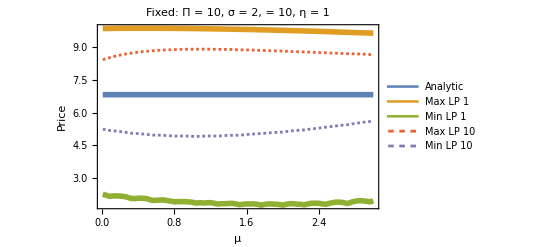

```mathematica
(*Different regularization and sigma parameter*)
regularization = 1;
sigma = 2;
pi = 10;
strike = 10;

title ="Fixed: " <> "Π = "  <> ToString[pi]<> ", σ = " <> ToString[sigma] <> ",  = " <> ToString[strike] <> ", η = " <> ToString[regularization] ;
pltmu2= Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, "InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, "InteriorPoint"],optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization, False, False,Automatic, Automatic]}, 
{mu,0.01, 3},
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01],Dashing[Tiny], Dashing[Tiny]},
 PlotLegends->{"Analytic", "Max LP "<>ToString[regularization], "Min LP "<>ToString[regularization],"Max LP "<>ToString[10*regularization], "Min LP "<>ToString[10*regularization]},FrameLabel->{"μ", "Price"}, LabelStyle->{FontSize->13},Frame->True,PlotRange->All, PlotLabel->title, PlotPoints->5]
Export[directory <> "pltmu2-sigma.pdf", pltmu2];
```

#### Scanning the volatility σ parameter

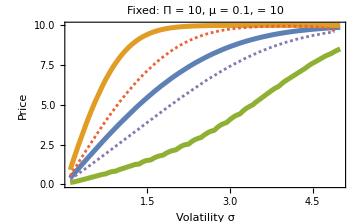

```mathematica
regularization = 1;
mu = 0.1;
pi = 10;
strike = 10;

title ="Fixed: " <> "Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ",  = " <> ToString[strike];

pltsigma4=Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True, False, Automatic, "InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic,"InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,True, False, Automatic, "InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,False, False, Automatic, "InteriorPoint"]}, 
{sigma, 0.1, 5}, (*PlotLegends->{"Analytic", "Max LP η = " <> ToString[regularization], "Min LP η = " <> ToString[regularization], "Max LP η = " <> ToString[10*regularization], "Min LP η = " <> ToString[10*regularization]},*) 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01], Dashing[Tiny], Dashing[Tiny]},
FrameLabel->{"Volatility σ", "Price"}, LabelStyle->{FontSize->13},Frame->True,PlotLabel->title, PlotPoints->5,ImageSize->360]
Export[directory <> "pltsigma4.pdf", pltsigma4];
```

#### Scan strike price

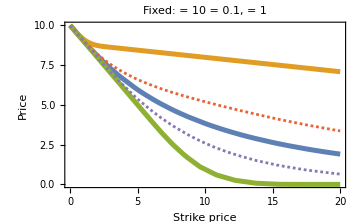

```mathematica
regularization = 1;
mu = 0.1;
sigma = 1;
pi = 10;

title ="Fixed: " <> " = "  <> ToString[pi]<> "  = " <>ToString[mu] <> ",  = " <>ToString[sigma]  ;

pltstrike3 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,True, False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,True, False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,False, False, Automatic, Automatic]}, 
{strike, 0, 20}, (*PlotLegends->{"Analytic", "Max LP η = " <> ToString[regularization], "Min LP η = " <> ToString[regularization], "Max LP η = " <> ToString[10*regularization], "Min LP η = " <> ToString[10*regularization]},*) 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01],Dashing[Tiny], Dashing[Tiny]},
FrameLabel->{"Strike price ", "Price"}, 
LabelStyle->{FontSize->13},
Frame->True,PlotLabel->title, PlotPoints->5, ImageSize->360]
Export[directory <> "pltstrike3.pdf", pltstrike3];
```

#### Scan the stock price

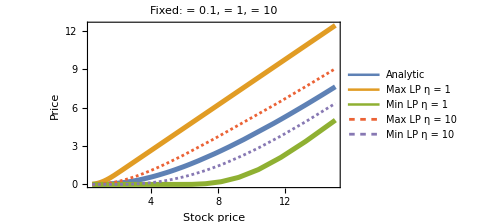

```mathematica
regularization = 1;
mu = 0.1;
sigma = 1;
strike = 10;

title ="Fixed: " <> " = " <>ToString[mu] <> ",  = " <>ToString[sigma] <> ",  = " <> ToString[strike] ;

pltstock2 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True,False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, 10*regularization,True,False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,False, False, Automatic, Automatic]}, 
{pi, 0.5, 15}, PlotLegends->Placed[{"Analytic", "Max LP η = " <> ToString[regularization], "Min LP η = " <> ToString[regularization], "Max LP η = " <> ToString[10*regularization], "Min LP η = " <> ToString[10*regularization]},{Left,Top}], 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01],Dashing[Tiny], Dashing[Tiny]}, 
LabelStyle->{FontSize->13},
Frame->True,
Axes->True,
FrameLabel->{"Stock price ", "Price"}, PlotLabel->title, PlotPoints->5, ImageSize->360]
Export[directory <> "pltstock2.pdf", pltstock2];
```